## y~N(μ,σ), μ,σ~p(μ,σ|Φ) -> y~N(0,1) ∫N(y|μ,σ)p(μ,σ|Φ)dμ dσ = N(y|0,1) The above, whilst true, is useless. How to sample from p(μ,σ|Φ)? p(y,μ,σ)=N(y|μ,σ)p(μ,σ|Φ) Also, the problem as stated above does not have unique solutions, as for example, μ=δ(0) and σ=δ(1) satisfies the RHS, but so does μ~N(0,1) and σ->0. Therefore we need priors, μ, σ ~ p(μ, σ|Ψ), where Ψ is known. So the aim is to find p(μ, σ | Ψ, Ξ), where Ξ is a shorthand for the parameters of the output distribution (here N(0, 1)). Can we use Bayes’ rule? p(μ, σ | Ψ, Ξ) = p(μ, σ | Ψ, Ξ) p(μ, σ | Ψ) No. What about the joint distribution, p(μ, σ , y | Ψ, Ξ) = p(μ, σ | Ψ, Ξ) p(y | Ξ) p(μ, σ , y | Ψ, Ξ) = p(y | μ, σ) p(μ, σ| Ψ, Ξ) Ermm. We know that in the limits n -> ∞, that p(μ,σ|y1,y2,..,yn, Ψ) -> p(μ, σ|Ψ, Ξ), where yi~N(0, 1)

```mathematica
n=100000;
muSamples=RandomVariate[UniformDistribution[{-4,4}],n];
sigmaSamples=RandomVariate[UniformDistribution[{0,1}],n];
y=RandomVariate[NormalDistribution[#1,#2],{1}][[1]]&@@@Thread[{muSamples,sigmaSamples}];
```

```mathematica
contourVolDist=SmoothKernelDistribution[y];
```

```mathematica
fStep[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposedMu=RandomVariate[NormalDistribution[μ,stepMu],{1}][[1]],proposedSigma=RandomVariate[NormalDistribution[σ,stepSigma],{1}][[1]]},{proposedMu,proposedSigma}]
fStepAndAccept[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposed=fStep[μ,σ,stepMu,stepSigma],u=RandomReal[]},If[Abs[proposed[[1]]]>1,{μ,σ},If[Or[proposed[[2]]<0,proposed[[2]]>3],{μ,σ},If[PDF[RandomVariate[NormalDistribution[proposed[[1]],proposed[[2]]],{1}][[1]],
```

## Try stepping around output space and accept / rejecting as in usual Metropolis, then simulating from the posterior p(μ,σ|y_i) for each accepted y_i

```mathematica
fStep[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposedMu=RandomVariate[NormalDistribution[μ,stepMu],{1}][[1]],proposedSigma=RandomVariate[NormalDistribution[σ,stepSigma],{1}][[1]]},{proposedMu,proposedSigma}]
fStepY[y_,stepY_]:=RandomVariate[NormalDistribution[y,stepY],{1}][[1]]
fStepAcceptY[y_,stepY_]:=Block[{proposed=fStepY[y,stepY],u=RandomReal[]},If[(PDF[NormalDistribution[0,1],proposed]/PDF[NormalDistribution[0,1],y])(PDF[contourVolDist,proposed]/PDF[contourVolDist,y])>u,proposed,y]]
fStepAndAccept[y_,μ_,σ_,stepMu_,stepSigma_]:=Block[{proposed=fStep[μ,σ,stepMu,stepSigma],u=RandomReal[]},If[Abs[proposed[[1]]]>1,{μ,σ},If[Or[proposed[[2]]<0,proposed[[2]]>3],{μ,σ},If[PDF[NormalDistribution[proposed[[1]],proposed[[2]]],y]/PDF[NormalDistribution[μ,σ],y]>u,proposed,{μ,σ}]]]]
fStepYAndMuSigma[y_,μ_,σ_,stepMu_,stepSigma_,stepY_]:=Block[{y1=fStepAcceptY[y,stepY]},Join[{y1}, fStepAndAccept[y1,μ,σ,stepMu,stepSigma]]]
fWeirdSampler[numIter_Integer,y_,μ_,σ_,stepMu_,stepSigma_,stepY_]:=NestList[fStepYAndMuSigma[#[[1]],#[[2]],#[[3]],stepMu,stepSigma,stepY]&,{y,μ,σ},numIter]
```

```mathematica
samples=fWeirdSampler[10000,0,0,1,0.5,0.5,0.5];
```

General::munfl: 1.44496 1.57565363756×10^-557 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.99675 1.5784571449×10^-6273 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 10.0202 5.81089743627×10^-2778 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

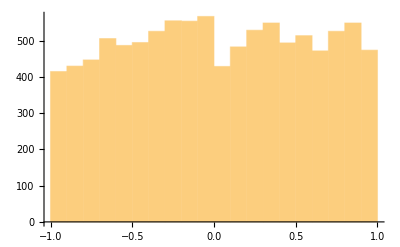

```mathematica
Histogram[samples[[All,2]]]
```

```mathematica
y=RandomVariate[NormalDistribution[#1,#2],{1}][[1]]&@@@samples[[All,{2,3}]];
```

```mathematica
StandardDeviation@y
```

1.76727

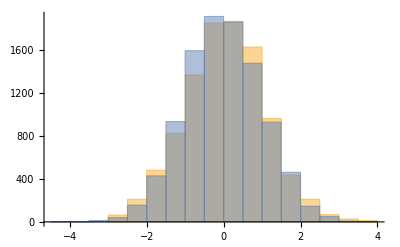

```mathematica
Histogram[{samples[[All,1]],RandomVariate[NormalDistribution[0,1],{Length@y}]}]
```

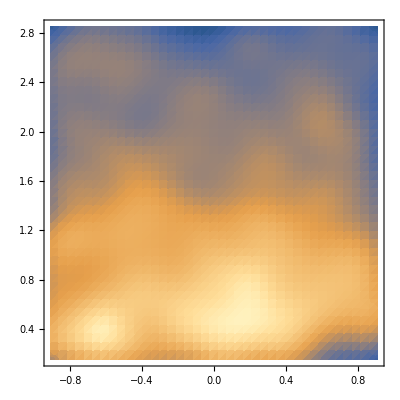

```mathematica
SmoothDensityHistogram[samples[[All,{2,3}]]]
```

## Trying Tarantola

```mathematica
fStep[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposedMu=RandomVariate[NormalDistribution[μ,stepMu],{1}][[1]],proposedSigma=σ},{proposedMu,proposedSigma}]
fEstimateIntegral[numsamples_Integer,μ_,σ_]:=Block[{d=RandomVariate[NormalDistribution[0,0.5],numsamples]},Mean[(PDF[NormalDistribution[μ,σ],#]/PDF[contourVolDist,#])&/@d]]
fStepAccept[μ_,σ_,stepMu_,stepSigma_,numsamples_Integer]:=Block[{proposed=fStep[μ,σ,stepMu,stepSigma],u=RandomReal[]},If[Abs[proposed[[1]]]>5,{μ,σ},If[Or[proposed[[2]]<0,proposed[[2]]>3],{μ,σ},If[(fEstimateIntegral[numsamples,proposed[[1]],proposed[[2]]]/fEstimateIntegral[numsamples,μ,σ])>u,proposed,{μ,σ}]]]]
fTarantola[numIter_Integer,μ_,σ_,stepMu_,stepSigma_,numsamples_Integer]:=NestList[fStepAccept[#[[1]],#[[2]],stepMu,stepSigma,numsamples]&,{μ,σ},numIter]
```

```mathematica
samples=ParallelTable[fTarantola[1000,0,0.5,0.4,0.4,1000],{i,1,4,1}];
```

```mathematica
samples=Flatten[samples,1];
```

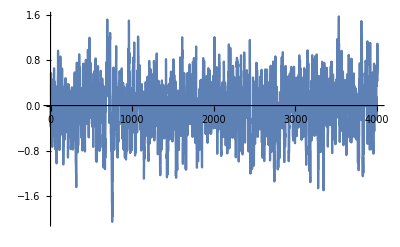

```mathematica
ListLinePlot[samples[[All,1]]]
```

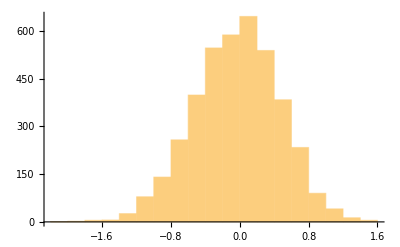

```mathematica
Histogram[samples[[All,1]]]
```

```mathematica
NIntegrate[PDF[NormalDistribution[0,1],x] PDF[NormalDistribution[0.5,1.2],x] / PDF[contourVolDist,x] ,{x,-10,10}]
```

1.10718

```mathematica
fEstimateIntegral[10000,0,3.2]
```

0.464276

## Start Tarantola again

```mathematica
n=100000;
muSamples=RandomVariate[UniformDistribution[{-1,1}],n];
y=RandomVariate[NormalDistribution[#1,0.1],{1}][[1]]&@@@muSamples;
contourVolDist=SmoothKernelDistribution[y];
```

```mathematica
fStep[μ_,σ_,stepMu_,stepSigma_]:=Block[{proposedMu=RandomVariate[NormalDistribution[μ,stepMu],{1}][[1]],proposedSigma=σ},{proposedMu,proposedSigma}]
fEstimateIntegral[numsamples_Integer,μ_,σ_]:=Block[{d=RandomVariate[NormalDistribution[0,0.1],numsamples]},Mean[(PDF[NormalDistribution[μ,σ],#]/PDF[contourVolDist,#])&/@d]]
fStepAccept[μ_,σ_,stepMu_,stepSigma_,numsamples_Integer]:=Block[{proposed=fStep[μ,σ,stepMu,stepSigma],u=RandomReal[]},If[Abs[proposed[[1]]]>5,{μ,σ},If[Or[proposed[[2]]<0,proposed[[2]]>3],{μ,σ},If[(fEstimateIntegral[numsamples,proposed[[1]],proposed[[2]]]/fEstimateIntegral[numsamples,μ,σ])>u,proposed,{μ,σ}]]]]
fTarantola[numIter_Integer,μ_,σ_,stepMu_,stepSigma_,numsamples_Integer]:=NestList[fStepAccept[#[[1]],#[[2]],stepMu,stepSigma,numsamples]&,{μ,σ},numIter]
```

```mathematica
samples=ParallelTable[fTarantola[100,0,0.1,0.4,0.4,100],{i,1,4,1}];
samples=Flatten[samples,1];
```

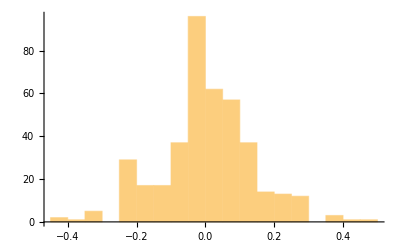

```mathematica
Histogram[samples[[All,1]]]
```

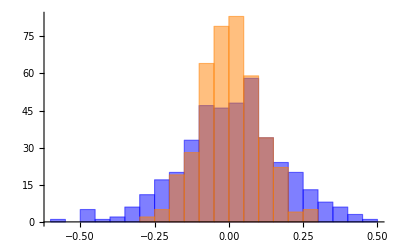

```mathematica
Histogram[{RandomVariate[NormalDistribution[#1,#2],{1}][[1]]&@@@samples,RandomVariate[NormalDistribution[0,0.1],{Length@samples}]},ChartStyle->{Blue,Orange}]
```

## Fredholm equation

```mathematica
eqn = PDF[NormalDistribution[0,1],d] == Integrate[PDF[NormalDistribution[mu,0.1],d] p[mu],{mu,-∞,∞}]
```

(ⅇ^(-d^2/2))/(√(2 π))==∫_(-∞)^∞ 3.98942 ⅇ^(-50. (d-mu)^2) p[mu]ⅆmu

```mathematica
sol=DSolveValue[eqn,p[x],x]
```

DSolveValue[(ⅇ^(-d^2/2))/(√(2 π))==∫_(-∞)^∞ 3.98942 ⅇ^(-50. (d-mu)^2) p[mu]ⅆmu,p[x],x]

## Answer from Stack exchange

```mathematica
Integrate[PDF[NormalDistribution[mu,1/10],d] PDF[NormalDistribution[0,Sqrt[99/100]],mu],{mu,-∞,∞}]
```

$Aborted

```mathematica
N@Sqrt[99/100]
```

0.994987

```mathematica
n=10000;
muSamples=RandomVariate[NormalDistribution[0,Sqrt[99/100]],{n}];
d=RandomVariate[NormalDistribution[#,0.1],{1}][[1]]&/@muSamples;
```

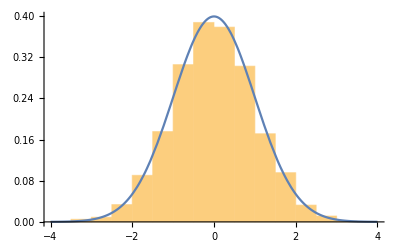

```mathematica
Show[Histogram[d,Automatic,"PDF"],Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

```mathematica
test=Table[{d,NIntegrate[PDF[NormalDistribution[0,Sqrt[99/100]],mu] PDF[NormalDistribution[mu,1/10],d] ,{mu,-∞,∞}]},{d,-4,4,0.1}];
```

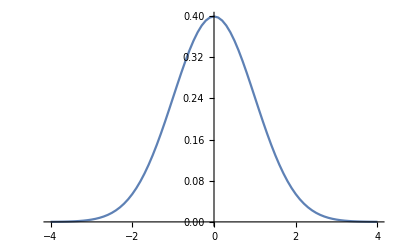

```mathematica
ListLinePlot[test]
```

## Troy’s consistent marginals - with fixed noise

```mathematica
n=100000;
muSamples=RandomVariate[UniformDistribution[{-3,3}],n];
q=RandomVariate[NormalDistribution[#1,0.8],{1}][[1]]&/@muSamples;
data=PDF[NormalDistribution[0,1],#]&/@q;
```

```mathematica
dens=SmoothKernelDistribution[q];
pfprior=PDF[dens,#]&/@q;
ratio=data/pfprior;
```

```mathematica
lnormrat=ratio/Max[ratio];
```

```mathematica
muKept=Table[If[lnormrat[[i]]>RandomReal[],{q[[i]],muSamples[[i]]},-1],{i,1,Length@lnormrat}];
```

```mathematica
muFinal=DeleteCases[muKept,-1];
```

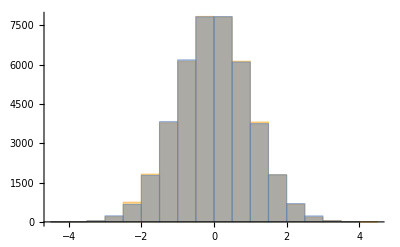

```mathematica
Histogram[{muFinal[[All,1]],RandomVariate[NormalDistribution[0,1],{Length@muFinal}]}]
```

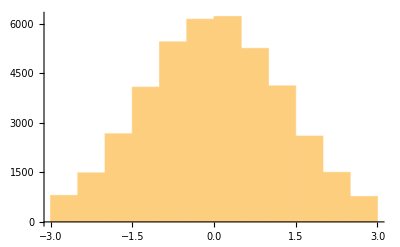

```mathematica
Histogram[muFinal[[All,2]]]
```

### Testing

```mathematica
qTest=RandomVariate[NormalDistribution[#,0.8],{1}][[1]]&/@muFinal[[All,2]];
```

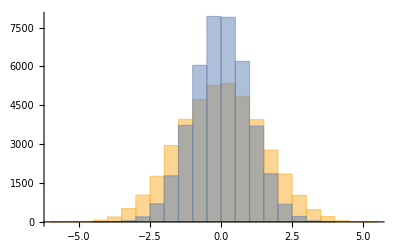

```mathematica
Histogram[{qTest,RandomVariate[NormalDistribution[0,1],{Length@qTest}]}]
```

## Testing on stochastic decay with production

```mathematica
fCalculateA0[A_,t_,k1_,k2_]:=Block[{a0=A k1 + k2,r1=RandomReal[],r2=RandomReal[],τ},τ=(1/a0)Log[1/r1];If[r2<k2/a0,{t+τ,A+1},{t+τ,A-1}]]
fGillespie[A0_,k1_,k2_,tmax_]:=NestWhileList[fCalculateA0[#[[2]],#[[1]],k1,k2]&,{0,A0},#[[1]]<tmax&]
fInterpolationCorrect[f_,tobs_]:=f[tobs]+1
fGillespie10[A0_,k1_,k2_]:=Block[{samples=fGillespie[A0,k1,k2,10],f},f=Interpolation[samples,InterpolationOrder->1];If[f[10]>0,f[10],0.000001]]
```

```mathematica
test=fGillespie[0,0.1,1,100];
```

```mathematica
f=Interpolation[test,InterpolationOrder->1];
```

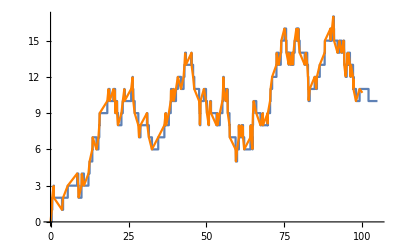

```mathematica
Show[ListStepPlot[test],Plot[f[t],{t,0,100},PlotStyle->Orange]]
```

```mathematica
test=Table[fGillespie10[0,0.15+0.1 RandomReal[],1],{10000}];
```

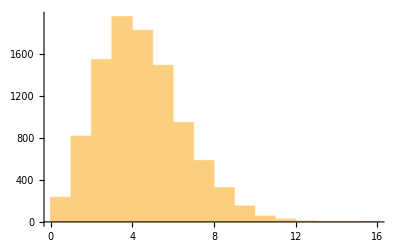

```mathematica
Histogram[test]
```

```mathematica
target=SmoothKernelDistribution[test];
n=100000;
k1=RandomVariate[UniformDistribution[{0,1}],n];
q1=ParallelTable[fGillespie10[0,k1[[i]],1],{i,1,Length@k1,1}];
```

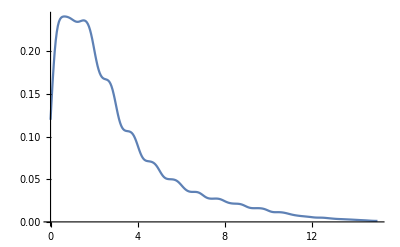

```mathematica
dens1=SmoothKernelDistribution[q1];
Plot[PDF[dens1,x],{x,0,15}]
```

```mathematica
data1=ParallelTable[PDF[target,q1[[i]]],{i,1,Length@q1,1}];
pfprior1=ParallelTable[PDF[dens1,q1[[i]]],{i,1,Length@q1,1}];
ratio=data1/pfprior1;
lnormrat=ratio/Max[ratio];
muKept=Table[If[lnormrat[[i]]>RandomReal[],{q1[[i]],k1[[i]]},-1],{i,1,Length@lnormrat}];
muFinal=DeleteCases[muKept,-1];
```

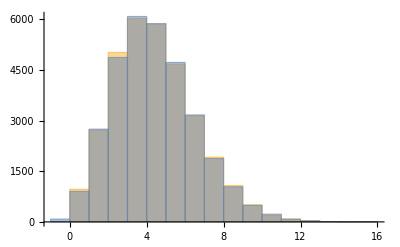

```mathematica
Histogram[{muFinal[[All,1]],RandomVariate[target,{Length@muFinal}]}]
```

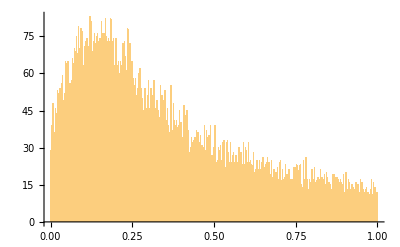

```mathematica
Histogram[muFinal[[All,2]],1000]
```

### Testing

```mathematica
qTest=ParallelTable[fGillespie10[0,muFinal[[All,2]][[i]],1],{i,1,Length@muFinal[[All,2]],1}];
```

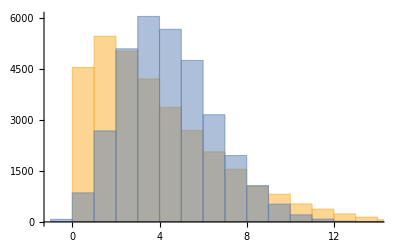

```mathematica
Histogram[{qTest,RandomVariate[target,{Length@qTest}]}]
```